```mathematica
data={{128,5},{64,4.98},{32,4.88},{16,4.58},{8,3.77},{4,2.51},{2,1.4},{1,0.729},{0.5,0.374},{0.25,0.184}}
```

{{128,5},{64,4.98},{32,4.88},{16,4.58},{8,3.77},{4,2.51},{2,1.4},{1,0.729},{0.5,0.374},{0.25,0.184}}

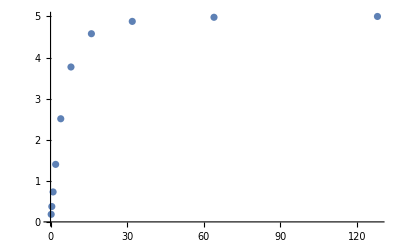

```mathematica
ListPlot[data]
```

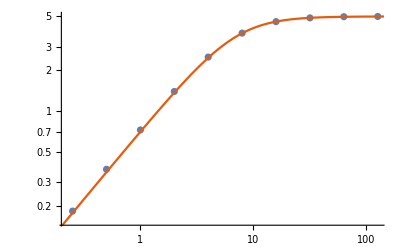

```mathematica
V0=5;
fc=7;
V[f_]:=f*V0/Sqrt[f^2+fc^2];
Show[ListLogLogPlot[data],LogLogPlot[V[x],{x,0,150},PlotTheme->"Scientific",PlotLabel->{Style["Frequency (Hz)",16],Style["CycleRMS (volts)",16]}]]
```